```mathematica
neightbours []:=Block[{result=Association[],colors={Red,Blue,Green,Darker[Yellow],Black}},

Table[
result[v]={}
,{v,VertexList[pl8]}
];
Table[
Table[
If[EdgeQ[pl8,UndirectedEdge[v,v2]],
result[v]=Append[result[v],Style[v2,colors[[v2]],12]]
]
,{v2,{1,2,3,4,5}}
]
,{v,VertexList[pl8]}
];
result
]
```

```mathematica
neightbours[]
```

<|12→{},13→{3},7→{},15→{1},17→{1,2},6→{2,3},3→{2,4},8→{3,4},9→{4},10→{},11→{1,5},1→{2,5},2→{1,3},14→{1,2,3,4,5},4→{3,5},16→{4,5},5→{1,4}|>

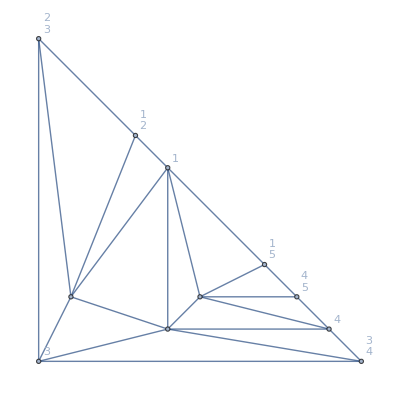

```mathematica
pl8Bis=With[
{rules=neightbours[]},
Graph[VertexDelete[pl8,{1,2,3,4,5,14}],VertexLabels->Table[v->Column[rules[v]],{v,VertexList[pl8]}]]
]
```